# Lista 3

## Exercise 1

We want to proof a theorem for a general 3x3 matrix:

```mathematica
ClearAll[A,a,b,c,d,e,f,g,h,i]
A={{a,b,c},{d,e,f},{g,h,i}}
FullSimplify[MatrixPower[A,3]-Tr[A]MatrixPower[A,2]+1/2((Tr[A])^2-Tr[MatrixPower[A,2]])A-Det[A]IdentityMatrix[3]]==0
```

{{a,b,c},{d,e,f},{g,h,i}}

{{0,0,0},{0,0,0},{0,0,0}}==0

## Exercise 2

We want to proof a theorem for two general 2x2 matrices:

```mathematica
ClearAll[A,B,a,b,c,d,e,f,g,h]
A={{a,b},{c,d}}
B={{e,f},{g,h}}
FullSimplify[(Tr[A.B]-Tr[A]Tr[B])+Tr[B]A+Tr[A]B-A.B-B.A]//MatrixForm
```

{{a,b},{c,d}}

{{e,f},{g,h}}

(0 | -d e+c f+b g-a h
-d e+c f+b g-a h | 0)

## Exercise 3

We want to compute rankt of the matrices and find their biggest minor:

```mathematica
M1={{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}
MatrixRank[M1]
Minors[M1,MatrixRank[M1]]
```

{{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

```mathematica
M2={{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}
MatrixRank[M2]
Minors[M1,MatrixRank[M2]]
```

{{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

## Exercise 4

We present a table witch names of European Capital Cities and their temperature:

```mathematica
TmpCapt=CountryData["Europe","CapitalCity"];
TC=Table[TmpCapt[[i]][[2]][[1]],{i,1,Length[TmpCapt]}];
tc[u_]:=WeatherData[u,"Temperature"];
FinalCT=Map[tc,TC];
FinalData=Transpose[{TC,FinalCT}];
TableForm[FinalData,TableHeadings->{Table[" ",{k,1,Length[FinalData]}],{" "," "}}]
```

|   |  
  | Tirana | 13.
  | AndorraLaVella | 8.5
  | Vienna | 0.4
  | Minsk | -1.1
  | Brussels | 5.4
  | Sarajevo | 1.
  | Sofia | 6.
  | Zagreb | 2.
  | Nicosia | 21.4
  | Prague | -0.1
  | Copenhagen | 4.
  | Tallinn | 3.
  | Torshavn | 3.5
  | Helsinki | 5.
  | Paris | 8.
  | Berlin | 2.6
  | Gibraltar | 14.6
  | Athens | 19.8
  | SaintPeterPort | 12.
  | Budapest | 0.5
  | Reykjavik | 3.
  | Dublin | 9.
  | Douglas | 10.
  | Rome | 6.
  | SaintHelier | 11.
  | Pristina | 4.
  | Riga | 0.
  | Vaduz | 0.8
  | Vilnius | 0.
  | Luxemburg | 4.
  | Skopje | 7.
  | Valletta | 15.
  | Chisinau | 3.
  | MonacoVille | 9.
  | Podgorica | 10.8
  | Amsterdam | 7.
  | Oslo | 1.7
  | Warsaw | 0.
  | Lisbon | 14.3
  | Bucharest | 3.
  | SanMarino | 14.
  | Belgrade | 2.4
  | Bratislava | 1.
  | Ljubljana | 0.2
  | Madrid | 11.
  | Longyearbyen | -3.9
  | Stockholm | 4.
  | Bern | 1.4
  | Kiev | 0.
  | London | 9.
  | VaticanCity | 6.

## Exercise 5

We want to compute rankt of the matrix:

```mathematica
la={{7-λ,-12,6},{10,-λ-19,10},{12,-24,13-λ}}
Det[la]
MatrixRank[la]
```

{{7-λ,-12,6},{10,-19-λ,10},{12,-24,13-λ}}

-1+λ+λ^2-λ^3

3

## Exercise 6

{{1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,1,4,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,4,6,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,9,8,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0},{8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0},{4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0},{1,4,3,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0},{9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Sum::argmu: Sum called with 1 argument; 2 or more arguments are expected.

General::stop: Further output of Sum :: argmu will be suppressed during this calculation.

DiscretePlot::argr: DiscretePlot called with 1 argument; 2 arguments are expected.

DiscretePlot[Null,Ticks→Range[0,9,1]]

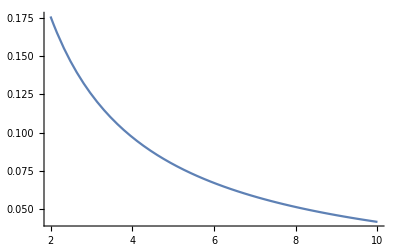

```mathematica
TDigits=Map[RealDigits,FinalCT[[All,1]]];
TDigits[[All,1]]
EqN[n_,x_]:=If[n==x,1,0]
Table[Sum[Map[Eqn[k,#],TDigits[[All,1]]],{i,1,Length[]}],{k,1,9}];
Temps=DiscretePlot[,Ticks->Range[0,9,1]]
Theorem=Plot[Log10[1+1/x],{x,2,10}];
Show[Theorem]
```

```mathematica
Pop=CountryData[,"Population"]
```

## Exercise 7

## Exercise 8

## Exercise 9